This notebook illustrates Example 1 of the paper.

```mathematica
u = {u1, u2}
Xdomain = -2 <= x <= 2
```

{u1,u2}

-2≤x≤2

Define the desired control input and the constraints

```mathematica
Subscript[π, des] = {-2, 0}

a1 = {1, 0}
b1 = 1
a2 = {-1, -x}
b2 = -1 -x

Subscript[cons, QP] = {a1.u <= b1, a2.u <= b2}
```

{-2,0}

{1,0}

1

{-1,-x}

-1-x

{u1≤1,-u1-u2 x≤-1-x}

Define the feasible solution

```mathematica
Subscript[π, f] =  {1 - x^2 ,  1 + 2 x}
```

{1-x^2,1+2 x}

Check the feasible solution

```mathematica
Simplify[Subscript[cons, QP] /.{u1 -> Subscript[π, f] [[1]], u2 -> Subscript[π, f] [[2]]}, Xdomain]
```

{True,True}

Get the analytic solution to the QP

```mathematica
Subscript[π, qp] = ArgMin[{(u-Subscript[π, des]).(u-Subscript[π, des]), Subscript[cons, QP]}, u]
```

{Piecewise[{{-2, x≤-3}, {(1+x-2 x^2)/(1+x^2), x>1/3||-3<x≤0}, {(1+x-2 x^2-√((x^2 (-1+3 x)^2)/((1+x^2)^2))-x^2 √((x^2 (-1+3 x)^2)/((1+x^2)^2)))/(1+x^2), True}}],Piecewise[{{-√((9 x^2+6 x^3+x^4)/((1+x^2)^2)), -3<x≤0}, {√((9 x^2+6 x^3+x^4)/((1+x^2)^2)), x>1/3}, {√(6-4 ((1+x-2 x^2)/(1+x^2)-√((x^2-6 x^3+9 x^4)/((1+x^2)^2)))-((1+x-2 x^2)/(1+x^2)-√((x^2-6 x^3+9 x^4)/((1+x^2)^2)))^2), 0<x≤1/3}, {0, True}}]}

```mathematica
Simplify[Subscript[π, qp], Xdomain]
```

{Piecewise[{{1, 0<x≤1/3}, {(1+x-2 x^2)/(1+x^2), True}}],Piecewise[{{1, 0<x≤1/3}, {(x (3+x))/(1+x^2), True}}]}

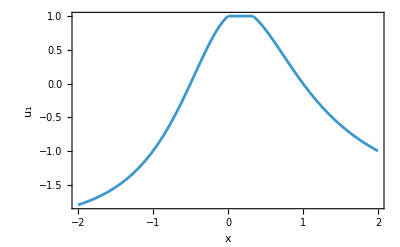

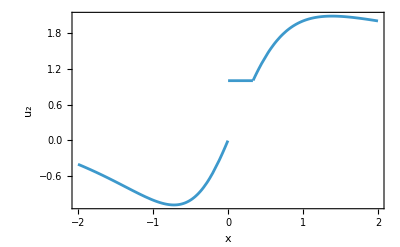

```mathematica
Plot[Subscript[π, qp][[1]], {x, -2, 2}, Frame->True, FrameLabel->{"x", "u_1"}]
Plot[Subscript[π, qp][[2]], {x, -2, 2}, Frame->True, FrameLabel->{"x", "u_2"}]
```

We can see a discontinuous jump in the solution.

Define the SOCP constraints

```mathematica
MyNorm[x_]:= Sqrt[x.x]
MyNormalize[x_]:= x/MyNorm[x]

r = Min[ (b1 - a1.Subscript[π, f])/MyNorm[a1], (b2- a2.Subscript[π, f])/MyNorm[a2]]
Subscript[cons, socp] = FullSimplify[{Sqrt[(u - Subscript[π, f]).(u - Subscript[π, f])] <= r} , Xdomain]
```

Min[x^2,(-x-x^2+x (1+2 x))/(√(1+x^2))]

{√((1+x^2) ((-1+u2-2 x)^2+(-1+u1+x^2)^2))≤x^2}

We can compute the analytic solution first

```mathematica
Subscript[π, socpanalytic] =FullSimplify[ Subscript[π, f] + Min[r, MyNorm[Subscript[π, des] -Subscript[π, f]]] MyNormalize[Subscript[π, des] -Subscript[π, f]], Xdomain]
```

{1-x^2+(x^2 (-3+x^2))/(√((1+x^2) (10+x (4-2 x+x^3)))),((1+2 x) (-x^2/(√(1+x^2))+√(10+x (4-2 x+x^3))))/(√(10+x (4-2 x+x^3)))}

```mathematica
Subscript[π, socpsolver] = Assuming[Xdomain, ArgMin[{(u-Subscript[π, des]).(u-Subscript[π, des]), Subscript[cons, socp]}, u, Reals]]
```

{(2-4 x-10 x^2-8 x^3-14 x^4-4 x^5+x^6-x^8+3 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))+2 x^2 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))-x^4 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2))))/(2 (1+x^2) (10+4 x-2 x^2+x^4))-1/2 √(1/((1+x^2)^2 (10+4 x-2 x^2+x^4)^2)(-36-192 x-400 x^2-528 x^3-584 x^4-368 x^5-92 x^6-40 x^7+36 x^8-24 x^9-76 x^10-16 x^11+15 x^12-4 x^13-4 x^14+12 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))+56 x ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))+100 x^2 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))+128 x^3 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))+152 x^4 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))+104 x^5 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))+66 x^6 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))+40 x^7 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))+10 x^8 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))+8 x^9 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))+8 x^10 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))-((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))^2-4 x ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))^2-6 x^2 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))^2-8 x^3 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))^2-9 x^4 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))^2-4 x^5 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))^2-4 x^6 ((6+4 x+4 x^2+4 x^3+x^6)/(1+x^2)-2 √((10 x^4+4 x^5-2 x^6+x^8)/(1+x^2)))^2)),Piecewise[{{-1/2 √((40+176 x+256 x^2+208 x^3+192 x^4+64 x^5+4 x^6+16 x^7+16 x^8-8 √((x^4 (10+4 x-2 x^2+x^4))/(1+x^2))-32 x √((x^4 (10+4 x-2 x^2+x^4))/(1+x^2))-40 x^2 √((x^4 (10+4 x-2 x^2+x^4))/(1+x^2))-32 x^3 √((x^4 (10+4 x-2 x^2+x^4))/(1+x^2))-32 x^4 √((x^4 (10+4 x-2 x^2+x^4))/(1+x^2)))/(10+4 x+8 x^2+4 x^3-x^4+x^6)), x≤-1/2}, {1/2 √((40+176 x+256 x^2+208 x^3+192 x^4+64 x^5+4 x^6+16 x^7+16 x^8-8 √((x^4 (10+4 x-2 x^2+x^4))/(1+x^2))-32 x √((x^4 (10+4 x-2 x^2+x^4))/(1+x^2))-40 x^2 √((x^4 (10+4 x-2 x^2+x^4))/(1+x^2))-32 x^3 √((x^4 (10+4 x-2 x^2+x^4))/(1+x^2))-32 x^4 √((x^4 (10+4 x-2 x^2+x^4))/(1+x^2)))/(10+4 x+8 x^2+4 x^3-x^4+x^6)), True}}]}

Check the analytic solution is same as what Mathematica thinks is the solution

```mathematica
FullSimplify[Subscript[π, socpanalytic] [[1]]==  Subscript[π, socpsolver][[1]], Xdomain]
```

True

```mathematica
FullSimplify[Subscript[π, socpanalytic] [[2]]==  Subscript[π, socpsolver][[2]], Xdomain]
```

True

Plot the solutions

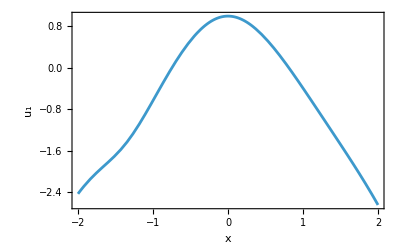

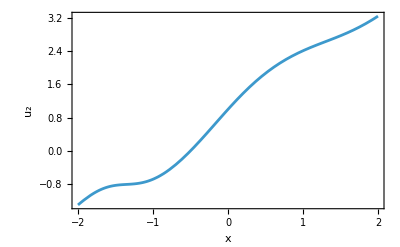

```mathematica
Plot[Subscript[π, socpanalytic][[1]], {x, -2, 2}, Frame->True, FrameLabel->{"x", "u_1"}]
Plot[Subscript[π, socpanalytic][[2]], {x, -2, 2}, Frame->True, FrameLabel->{"x", "u_2"}]
```

We can see that the solution of the SOCP is Lipschitz continuous . In fact, over the domain it is also differentiable.